```mathematica
Clear["Global`*"]
```

```mathematica
imag=y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7;

real = x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7;
```

```mathematica
xs = Solve[imag==0,x];
xs/.{y-> 0.01,μ-> μ0}
```

{{x→1/2},{x→0.154321},{x→0.845679},{x→0.329204},{x→0.670796},{x→0.0415067},{x→0.958493}}

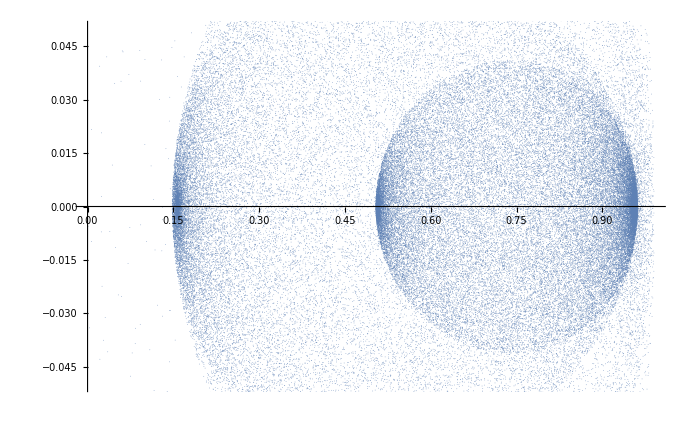
```mathematica
img5= -Graphics-;
```

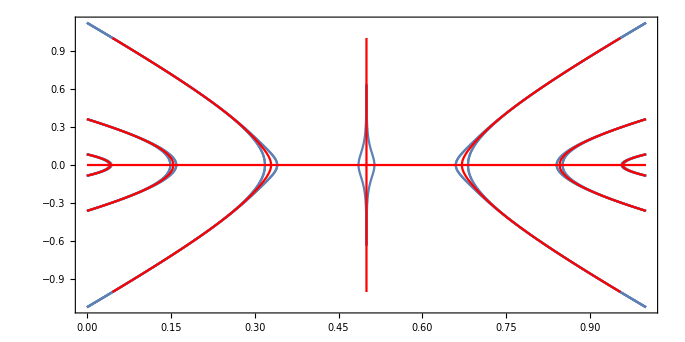
```mathematica
img4 = -Graphics-;
```

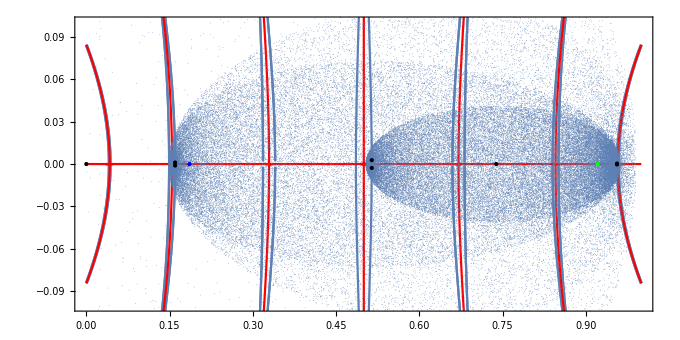
```mathematica
img6 =-Graphics-;
```

```mathematica
xsub = 0;
xsup = 0.04150665008970761;
Δx = (xsup-xsub)/100;
ysub = -0.01;
ysup = 0.01;
Δy = 0.01;
```

```mathematica
LISTA=Partition[Partition[Flatten[Table[{x,y},{x,xsub,xsup,Δx},{y,ysub,ysup,Δy}]],2],1];
DLISTA= Map[Directive,Partition[Flatten[Table[{Hue[x],PointSize[0.5Abs[y] +0.01],Opacity[1]},{x,0,1,0.85 1/((xsup-xsub)/Δx)},{y,ysub,ysup,Δy}]],3]];
MAPLISTA=Block[{μ= 3.82830},Partition[Partition[Flatten[Table[{real,imag},{x,xsub,xsup,Δx},{y,ysub,ysup,Δy}]],2],1]];
```

```mathematica
DLISTA
```

{Directive[{Hue[0.],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.0085],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.0085],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.0085],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.017],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.017],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.017],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.025500000000000002],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.025500000000000002],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.025500000000000002],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.034],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.034],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.034],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.0425],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.0425],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.0425],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.051000000000000004],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.051000000000000004],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.051000000000000004],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.059500000000000004],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.059500000000000004],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.059500000000000004],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.068],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.068],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.068],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.07650000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.07650000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.07650000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.085],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.085],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.085],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.0935],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.0935],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.0935],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.10200000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.10200000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.10200000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.11050000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.11050000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.11050000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.11900000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.11900000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.11900000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.1275],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.1275],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.1275],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.136],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.136],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.136],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.14450000000000002],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.14450000000000002],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.14450000000000002],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.15300000000000002],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.15300000000000002],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.15300000000000002],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.1615],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.1615],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.1615],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.17],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.17],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.17],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.17850000000000002],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.17850000000000002],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.17850000000000002],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.187],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.187],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.187],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.1955],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.1955],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.1955],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.20400000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.20400000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.20400000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.21250000000000002],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.21250000000000002],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.21250000000000002],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.22100000000000003],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.22100000000000003],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.22100000000000003],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.2295],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.2295],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.2295],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.23800000000000002],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.23800000000000002],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.23800000000000002],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.24650000000000002],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.24650000000000002],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.24650000000000002],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.255],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.255],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.255],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.2635],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.2635],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.2635],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.272],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.272],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.272],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.2805],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.2805],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.2805],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.28900000000000003],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.28900000000000003],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.28900000000000003],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.29750000000000004],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.29750000000000004],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.29750000000000004],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.30600000000000005],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.30600000000000005],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.30600000000000005],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.3145],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.3145],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.3145],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.323],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.323],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.323],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.3315],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.3315],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.3315],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.34],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.34],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.34],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.34850000000000003],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.34850000000000003],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.34850000000000003],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.35700000000000004],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.35700000000000004],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.35700000000000004],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.36550000000000005],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.36550000000000005],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.36550000000000005],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.374],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.374],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.374],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.3825],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.3825],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.3825],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.391],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.391],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.391],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.3995],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.3995],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.3995],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.40800000000000003],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.40800000000000003],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.40800000000000003],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.41650000000000004],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.41650000000000004],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.41650000000000004],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.42500000000000004],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.42500000000000004],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.42500000000000004],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.43350000000000005],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.43350000000000005],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.43350000000000005],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.44200000000000006],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.44200000000000006],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.44200000000000006],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.4505],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.4505],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.4505],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.459],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.459],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.459],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.4675],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.4675],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.4675],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.47600000000000003],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.47600000000000003],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.47600000000000003],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.48450000000000004],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.48450000000000004],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.48450000000000004],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.49300000000000005],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.49300000000000005],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.49300000000000005],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.5015000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.5015000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.5015000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.51],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.51],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.51],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.5185000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.5185000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.5185000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.527],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.527],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.527],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.5355000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.5355000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.5355000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.544],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.544],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.544],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.5525],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.5525],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.5525],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.561],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.561],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.561],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.5695],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.5695],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.5695],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.5780000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.5780000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.5780000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.5865],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.5865],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.5865],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.5950000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.5950000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.5950000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.6035],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.6035],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.6035],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.6120000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.6120000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.6120000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.6205],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.6205],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.6205],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.629],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.629],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.629],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.6375000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.6375000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.6375000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.646],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.646],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.646],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.6545000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.6545000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.6545000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.663],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.663],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.663],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.6715000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.6715000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.6715000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.68],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.68],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.68],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.6885],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.6885],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.6885],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.6970000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.6970000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.6970000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.7055],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.7055],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.7055],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.7140000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.7140000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.7140000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.7225],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.7225],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.7225],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.7310000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.7310000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.7310000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.7395],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.7395],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.7395],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.748],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.748],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.748],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.7565000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.7565000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.7565000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.765],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.765],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.765],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.7735000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.7735000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.7735000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.782],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.782],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.782],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.7905000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.7905000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.7905000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.799],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.799],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.799],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.8075000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.8075000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.8075000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.8160000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.8160000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.8160000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.8245],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.8245],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.8245],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.8330000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.8330000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.8330000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.8415],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.8415],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.8415],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.8500000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.8500000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.8500000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.8585],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.8585],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.8585],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.8670000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.8670000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.8670000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.8755000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.8755000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.8755000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.8840000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.8840000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.8840000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.8925000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.8925000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.8925000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.901],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.901],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.901],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.9095000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.9095000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.9095000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.918],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.918],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.918],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.9265000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.9265000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.9265000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.935],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.935],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.935],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.9435000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.9435000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.9435000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.9520000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.9520000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.9520000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.9605],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.9605],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.9605],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.9690000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.9690000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.9690000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.9775],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.9775],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.9775],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.9860000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.9860000000000001],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.9860000000000001],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.9945],PointSize[0.015],Opacity[1]}],Directive[{Hue[0.9945],PointSize[0.01],Opacity[1]}],Directive[{Hue[0.9945],PointSize[0.015],Opacity[1]}]}

```mathematica
ListPlot[LISTA⟦All,All,1;;2⟧,Frame->True];
```

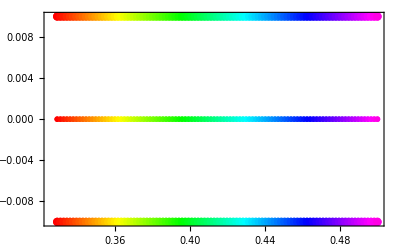

```mathematica
IMGoriginal= ListPlot[LISTA⟦All,All,1;;2⟧,PlotStyle->DLISTA,Frame->True]
```

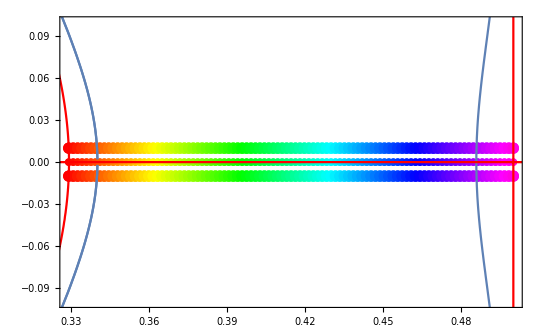

```mathematica
Show[IMGoriginal,img4, PlotRange-> {{0.32920392440925045, 0.5},{-0.1,0.1}}]
```

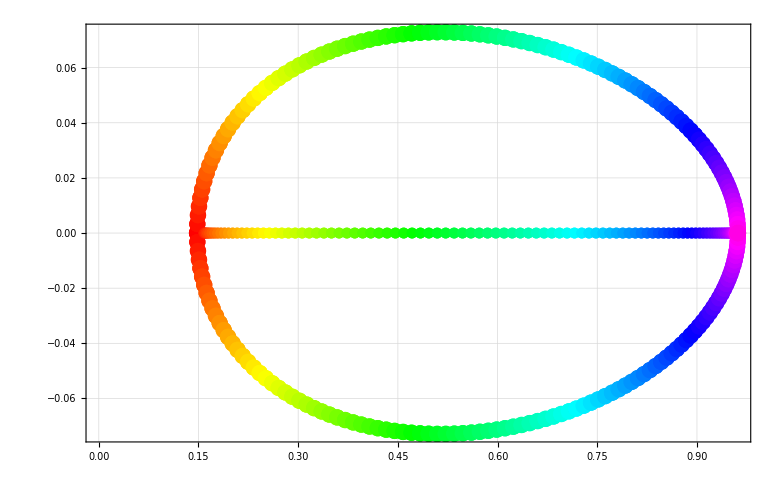

```mathematica
IMGColour = ListPlot[MAPLISTA⟦All,All,1;;2⟧,Frame->True,PlotStyle->DLISTA, PlotRange-> Automatic, GridLines->Automatic]
```

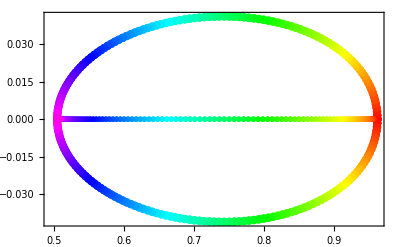

```mathematica
cicle1 = ListPlot[MAPLISTA⟦All,All,1;;2⟧,Frame->True,PlotStyle->DLISTA, PlotRange-> Automatic]
```

```mathematica
cicle2 = ListPlot[MAPLISTA⟦All,All,1;;2⟧,Frame->True,PlotStyle->DLISTA, PlotRange-> Automatic];
```

```mathematica
cicle3 = ListPlot[MAPLISTA⟦All,All,1;;2⟧,Frame->True,PlotStyle->DLISTA, PlotRange-> Automatic];
```

```mathematica
rest = ListPlot[MAPLISTA⟦All,All,1;;2⟧,Frame->True,PlotStyle->DLISTA, PlotRange-> Automatic];
```

```mathematica
cicle1
```

-Graphics-

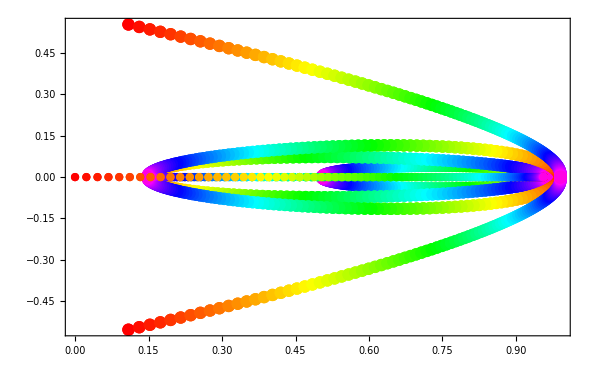

```mathematica
Show[cicle1,cicle2,cicle3, rest, PlotRange-> Automatic]
```

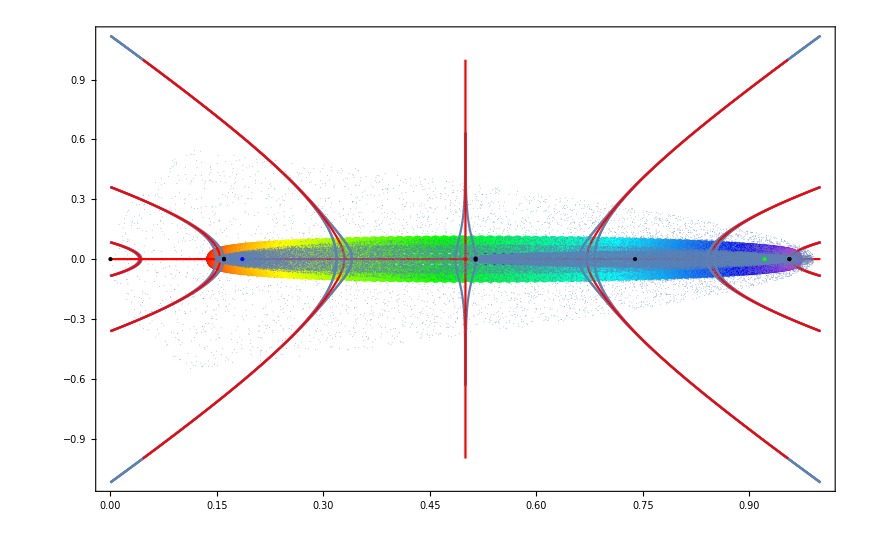

```mathematica
Show[cicle1,cicle2,img6, PlotRange-> Automatic]
```

```mathematica
lsolve= Solve[re== x/.{y-> 0,μ-> 3.82843},{x}]
```

{{x→0.},{x→0.15977},{x→0.160087},{x→0.513942},{x→0.514769},{x→0.738796},{x→0.956272},{x→0.956363}}

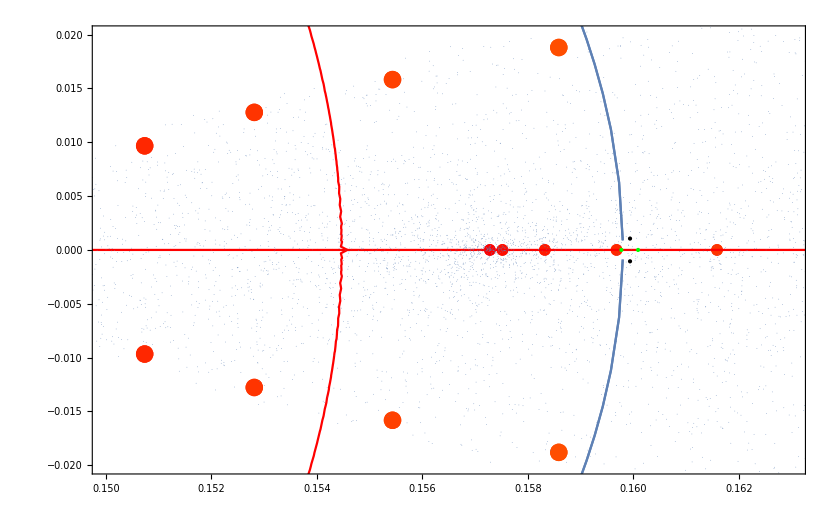

```mathematica
Show[cicle2,img6,Graphics[{PointSize[Large],Green, Point[{0.16008745209438813,0}],Point[{0.159769931608329,0}]}], PlotRange-> {{0.150,0.163},{-0.02,0.02}}]
```

xsub = 0.45
xsup = 0.6
ysub = 0
ysup = 0.1

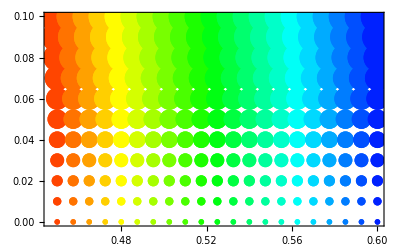

```mathematica
IMGoriginal
```

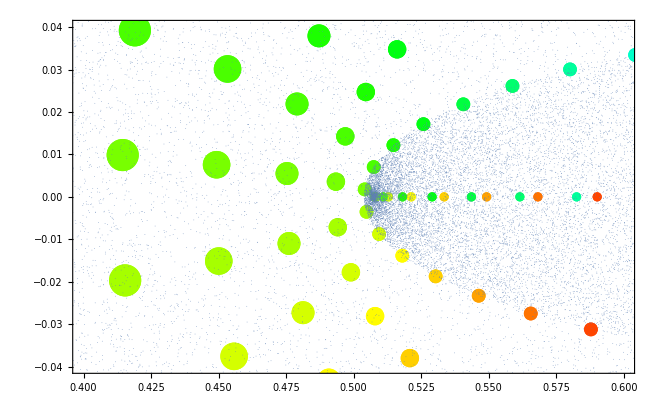

```mathematica
Show[IMGColour,img5, PlotRange-> {{0.4,0.6},{-0.04,0.04}}]
```

xsub = 0.45
xsup = 0.6
ysub = -0.1
ysup = 0

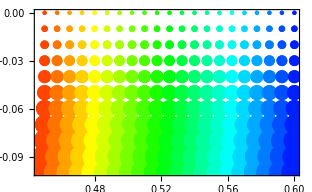

```mathematica
IMGoriginal
```

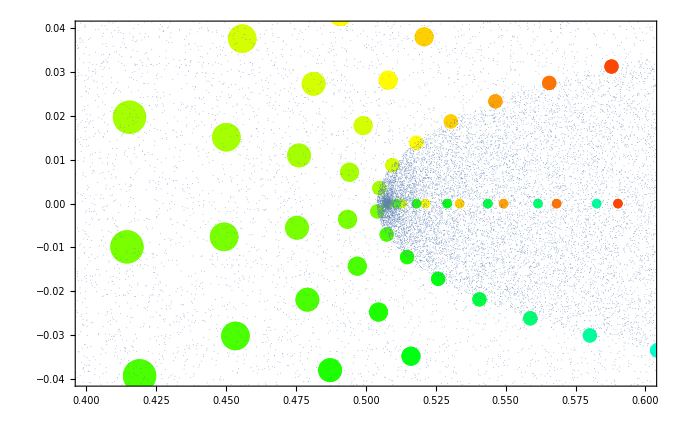

```mathematica
Show[IMGColour,img5, PlotRange-> {{0.4,0.6},{-0.04,0.04}}]
```

xsub = 0.45
xsup = 0.6
ysub = -0.1
ysup = 0.1

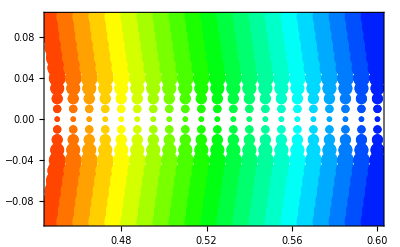

```mathematica
IMGoriginal
```

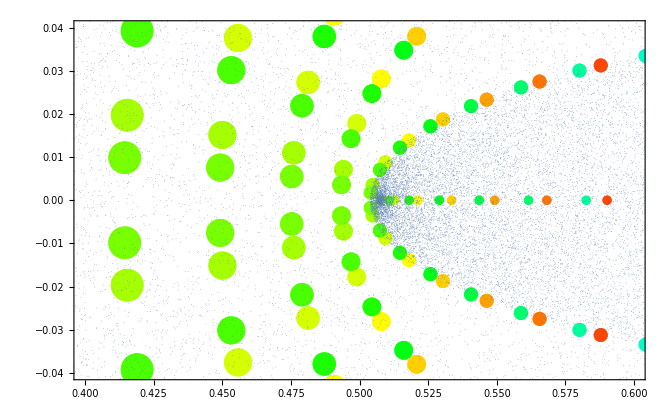

```mathematica
Show[IMGColour,img5, PlotRange-> {{0.4,0.6},{-0.04,0.04}}]
```

xsub = 0.45
xsup = 0.6
ysub = 0
ysup = 0.01

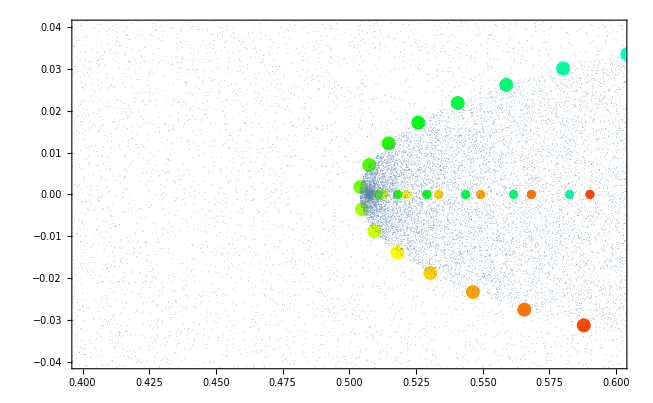

```mathematica
Show[IMGColour,img5, PlotRange-> {{0.4,0.6},{-0.04,0.04}}]
```

xsub = 0.5
xsup = 0.6
ysub = -0.01
ysup = 0.01

```mathematica
Show[IMGColour,img5, PlotRange-> {{0.4,0.6},{-0.04,0.04}}]
```

-Graphics-

de y_(n+1): x_n= f(f(x_n,x_(n+1)),y_(n+1))   (1)
   de x_(n+1): y_n= f(x_n,x_(n+1))    (2)

   aplicando (2) em (1):
 x_n= f(x_(n+1),y_(n+1)), o problema é isolar x_n

    se temos x_n= f(x_(n+1),y_(n+1)), por (2), temos y_n=f(x_(n+1),y_(n+1))

```mathematica
lsolve =Solve[xn == -yn1/(2 μ) (1/(√(xn1/μ+ xn^2-xn))) -1/2, xn];
```

```mathematica
curvaderivada =D[lsolve⟦1,1,2⟧,xn1]/.{μ-> 3.8283,yn1-> 0.01};
```

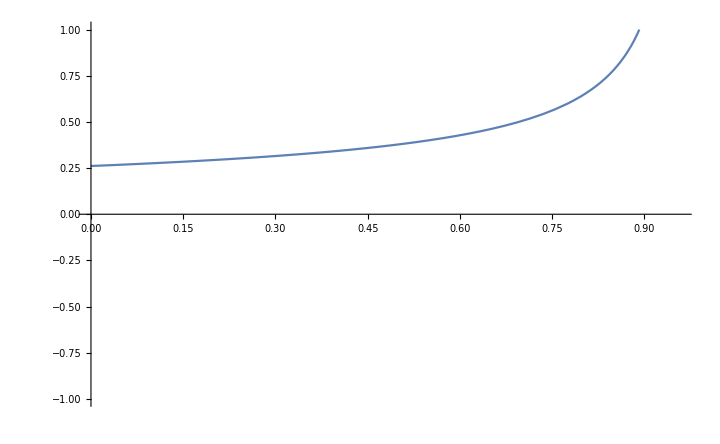

```mathematica
Plot[Chop[curvaderivada],{xn1,0,1}, PlotRange->{-1,1}]
```

```mathematica
curvaderivada/.xn1-> 0.7
```

0.0000189217+1.70308×10^-17 ⅈ

```mathematica
lsolve/.{xn1-> 0.51, yn1-> 0.01,μ-> 3.8283}
```

{{xn→0.158261+0. ⅈ},{xn→0.841735+0. ⅈ},{xn→-0.501388+0. ⅈ},{xn→-0.498608+0. ⅈ}}